```mathematica
ClearAll["Global'*"]
G[r1_,r2_]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G2[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
G3[{r1_,r2_}]:=3/40{{r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))},{r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))}};
```

```mathematica
g1[r1_,r2_]={r1^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2)),r1 r2/((r1^2+r2^2)^(3/2))};
g2[r1_,r2_]={r1 r2/((r1^2+r2^2)^(3/2)),r2^2/((r1^2+r2^2)^(3/2))+1/((r1^2+r2^2)^(1/2))};
```

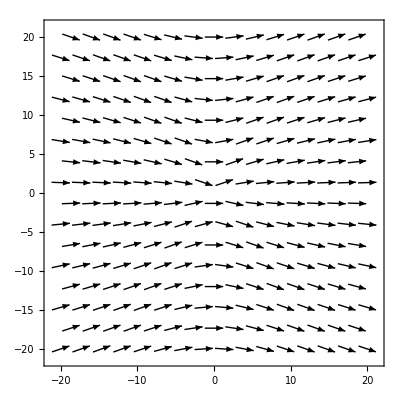

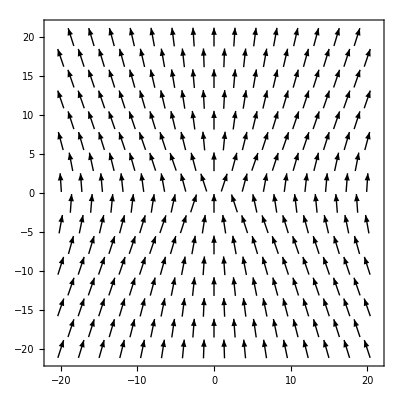

```mathematica
VectorPlot[g1[x,y],{x,-20,20},{y,-20,20}]
VectorPlot[g2[x,y],{x,-20,20},{y,-20,20}]
```

```mathematica
y0:={100,100}
```

```mathematica
y0hat:=y0/Norm[y0];
```

```mathematica
epsilon:=1/Norm[y0]
```

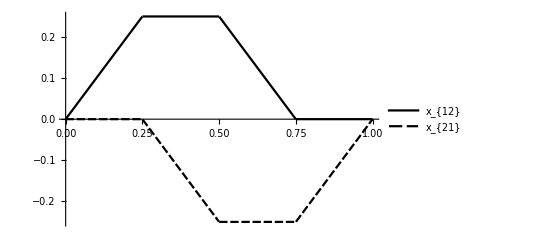

```mathematica
x1[t_]:={2,Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
x2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx1[t_]:={0,Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
dx2[t_]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
Plot[{x1[t][[2]],x2[t][[1]]},{t,0,1},PlotLegends->LineLegend[{"x_{12}","x_{21}"},LegendFunction->Frame]]
```

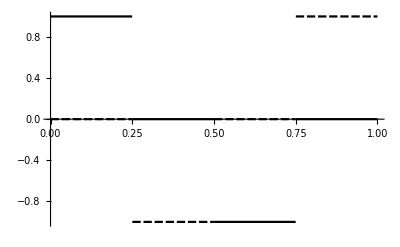

```mathematica
Plot[{dx1[t][[2]],dx2[t][[1]]},{t,0,1}]
```

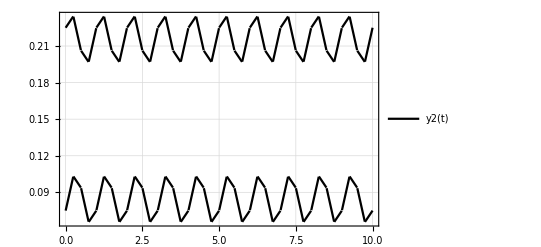

```mathematica
y2[t_]=G2[y0hat].x1[t]+ G2[y0hat].x2[t];
Plot[y2[t],{t,0,10},PlotTheme->"Detailed"]
y22=NDSolveValue[{y'[t]==(3/40)(y0hat.x1[t] dx1[t]+3 y0hat (y0hat.x1[t])(y0hat.dx1[t])+(y0hat.x2[t] )dx2[t]+3 y0hat (y0hat.x2[t])( y0hat.dx2[t]) - y0hat (x1[t].dx1[t])-y0hat (x2[t].dx2[t])-x1[t] (y0hat.dx1[t])-x2[t]( y0hat.dx2[t])),y[0]=={0,0}},y,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->25];
y23=NDSolveValue[{y'[t]==(3/40)(y2[t] y0hat.dx1[t]+y2[t] y0hat.dx2[t]+y0hat y2[t].(dx1[t]+dx2[t])-(dx1[t]+dx2[t])(y0hat.y2[t])-3(y2[t].y0hat)(y0hat.(dx1[t]+dx2[t])y0hat)),y[0]=={0,0}},y,{t,0,1},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->25];
```

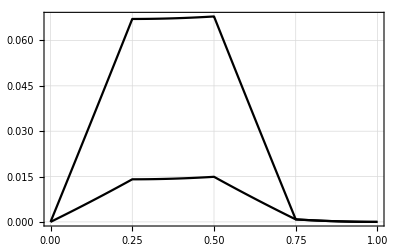

```mathematica
Plot[y22[t],{t,0,1},PlotTheme->"Detailed",PlotLegends->"y_{22}(t)"]
```

```mathematica
x11[t_?NumericQ]:={2,Piecewise[{{ Mod[t,1],0 ≤ Mod[t,1] ≤ 1/4},{1/4,1/4 ≤ Mod[t,1] ≤ 1/2},{1/4-( Mod[t,1]-1/2),1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
x21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-( Mod[t,1]-1/4),1/4 ≤ Mod[t,1] ≤ 1/2},{-1/4,1/2≤ Mod[t,1]≤ 3/4},{-1/4 + ( Mod[t,1]-3/4),3/4 ≤ Mod[t,1]≤ 1}}],0};
dx11[t_?NumericQ]:={0,Piecewise[{{1,0 ≤ Mod[t,1] ≤ 1/4},{0,1/4 ≤ Mod[t,1] ≤ 1/2},{-1,1/2≤ Mod[t,1]≤ 3/4},{0,3/4 ≤ Mod[t,1]≤ 1}}]};
dx21[t_?NumericQ]:={Piecewise[{{0,0 ≤ Mod[t,1] ≤ 1/4},{-1,1/4 ≤ Mod[t,1] ≤ 1/2},{0,1/2≤ Mod[t,1]≤ 3/4},{1,3/4 ≤ Mod[t,1]≤ 1}}],0};
y3=NDSolveValue[{b'[t]==G2[b[t]-x11[t]].dx11[t]+G2[b[t]-x21[t]].dx21[t],b[0]==y0},b,{t,0,10},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->25];
```

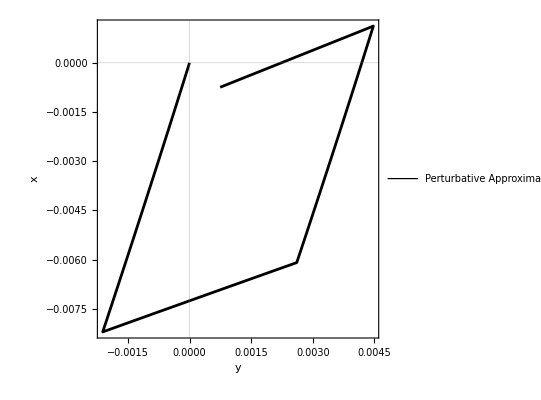

```mathematica
ParametricPlot[{y23[t]},{t,0,1},AspectRatio->1, FrameLabel->{"y","x"},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,PlotLegends->LineLegend[{"Perturbative Approximation"},LegendFunction->Frame],PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]}}]
```

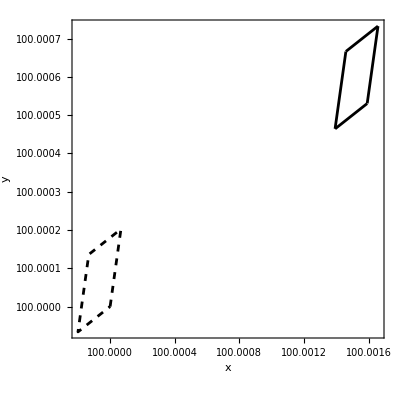

```mathematica
curve=ParametricPlot[{y0+epsilon y2[t]+epsilon^2 y22[t],y3[t]},{t,0,1},AspectRatio->1, FrameLabel->{"x","y"},PlotTheme->"Scientific",PerformanceGoal->"Quality",PlotRange->Full,PlotStyle->{{Black, Thickness[0.005]},{Dashed, Black,Thickness[0.005]}}]
```

```mathematica
dd1 =epsilon^2(y22[1.0]-y22[0])
y2[1]-y2[0]
dd2=y3[1]-y3[0]
dd3=epsilon^3(y23[1]-y23[0])
displ[h_]:=1/(Norm[h]^6)(27/2560)(0.1){h[[2]]^3+h[[2]]h[[1]]^2,-h[[1]]^3-h[[1]]h[[2]]^2}
dd4=N[displ[y0]]
Norm[dd4-dd3]
```

{2.32019×10^-21,7.62349×10^-21}

{0,0}

{2.67874345127×10^-10,-2.7221266737×10^-10}

{2.63671875000002724609375×10^-10,-2.63671875000004482421875×10^-10}

{2.63672×10^-10,-2.63672×10^-10}

5.26668×10^-24

```mathematica
curve2=ParametricPlot[{x1[t],x2[t]},{t,0,1}];
```

```mathematica
Animate[{Show[curve2,Graphics[{PointSize[Large],Point[x1[t]],Point[x2[t]]}]],Show[curve,Graphics[{PointSize[Large],Point[y0+epsilon y2[t]+epsilon^2 y22[t]]}]]},{t,0,1},RefreshRate->30];
y4=ParametricNDSolveValue[{b'[t] == G2[b[t] - x11[t]].dx11[t] + G2[b[t] - x21[t]].dx21[t], b[0] == {b1,b2}}, b[1]-b[0], {t, 0, 1},{b1,b2}, Method -> "StiffnessSwitching",  WorkingPrecision -> 25,PrecisionGoal->25,AccuracyGoal->25];
y4[100,100]
```

{2.69541037932×10^-10,-2.72126097119×10^-10}

```mathematica
y5=ParametricNDSolveValue[{y'[t]==(3/40)epsilon^2(y0hat.x1[t] dx1[t]+3 y0hat (y0hat.x1[t])(y0hat.dx1[t])+(y0hat.x2[t] )dx2[t]+3 y0hat (y0hat.x2[t])( y0hat.dx2[t]) - y0hat (x1[t].dx1[t])-y0hat (x2[t].dx2[t])-x1[t] (y0hat.dx1[t])-x2[t]( y0hat.dx2[t])),y[0]=={b1,b2}},y[1]-y[0],{t,0,1},{b1,b2},Method->"StiffnessSwitching",AccuracyGoal->15,PrecisionGoal->15,WorkingPrecision->25];
```

```mathematica
y21[t_,a_,b_]:=G[a,b].(x1[t]+x2[t]);
y6=Integrate[(3/4)(y21[t,q,p] {q,p}.dx1[t]+y21[t,q,p] {q,p}.dx2[t]+{q,p} y21[t,q,p] .(dx1[t]+dx2[t])-(dx1[t]+dx2[t])({q,p}.y21[t,q,p] )-3(y21[t,q,p] .{q,p})({q,p}.(dx1[t]+dx2[t]){q,p})),{t,0,1}]
```

{(27 (p^3+p q^2))/(2560 (p^2+q^2)^(3/2)),-(27 (p^2 q+q^3))/(2560 (p^2+q^2)^(3/2))}

```mathematica
mu=1;

Ginv[{r1_,r2_},a_]={{(2 (r1^2+2 r2^2))/(3 a √(r1^2+r2^2)),-(2 r1 r2)/(3 a √(r1^2+r2^2))},{-(2 r1 r2)/(3 a √(r1^2+r2^2)),(2 (2 r1^2+r2^2))/(3 a √(r1^2+r2^2))}};
```

```mathematica
K[{r1_,r2_},a_]={{(-81 a^4 (r1^2+r2^2)+18 a^2 (2 r1^2+r2^2)^2)/(4 (9 a^2 (5 r1^4+6 r1^2 r2^2+5 r2^4)-8 (r1^6+4 r1^4 r2^2+4 r1^2 r2^4+r2^6))),(9 a^2 (-2 r1^2 r2^2+9 a^2 (r1^2+r2^2)))/(4 (9 a^2 (5 r1^4+6 r1^2 r2^2+5 r2^4)-8 (r1^6+4 r1^4 r2^2+4 r1^2 r2^4+r2^6)))},{(9 a^2 (-2 r1^2 r2^2+9 a^2 (r1^2+r2^2)))/(4 (9 a^2 (5 r1^4+6 r1^2 r2^2+5 r2^4)-8 (r1^6+4 r1^4 r2^2+4 r1^2 r2^4+r2^6))),(-81 a^4 (r1^2+r2^2)+18 a^2 (r1^2+2 r2^2)^2)/(4 (9 a^2 (5 r1^4+6 r1^2 r2^2+5 r2^4)-8 (r1^6+4 r1^4 r2^2+4 r1^2 r2^4+r2^6)))}};
```

```mathematica
f1[t_]=K[x1[t]-x2[t],a].(Ginv[x1[t]-x2[t],a].dx1[t]-(Ginv[x1[t]-x2[t],a]^2).dx2[t]);
mat[{r1,r2},u]:=Simplify[Inverse[(1-Ginv[{r1,r2},u].Ginv[{r1,r2},u])].(1-Ginv[{r1,r2},u]).Ginv[{r1,r2},u]]
```

$Failed

```mathematica
{{(16 r1^6+3 r1^3 r2 (2 √(r1^2+r2^2)-9 u) u-3 r1 r2^3 u (10 √(r1^2+r2^2)+9 u)+4 (4 r2^6-3 r2^4 u (√(r1^2+r2^2)+3 u))+3 r1^4 (16 r2^2-u (8 √(r1^2+r2^2)+3 u))+r1^2 (48 r2^4-9 r2^2 u (4 √(r1^2+r2^2)+5 u)))/((r1^2+r2^2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))),(3 (4 r1^2+3 r1 r2+r2^2) u (2 r1 r2 √(r1^2+r2^2)+r1^2 (-4 √(r1^2+r2^2)+3 u)+r2^2 (-2 √(r1^2+r2^2)+3 u)))/((r1^2+r2^2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2)))},{(3 (r1^2+3 r1 r2+4 r2^2) u (2 r1 r2 √(r1^2+r2^2)+r2^2 (-4 √(r1^2+r2^2)+3 u)+r1^2 (-2 √(r1^2+r2^2)+3 u)))/((r1^2+r2^2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))),(16 r1^6+16 r2^6+3 r1 r2^3 (2 √(r1^2+r2^2)-9 u) u-3 r2^4 u (8 √(r1^2+r2^2)+3 u)-3 r1^3 r2 u (10 √(r1^2+r2^2)+9 u)+12 r1^4 (4 r2^2-u (√(r1^2+r2^2)+3 u))+r1^2 (48 r2^4-9 r2^2 u (4 √(r1^2+r2^2)+5 u)))/((r1^2+r2^2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2)))}}
series[f_,var:{_Symbol..},n_Integer?Positive]:=Module[{s},Expand@Normal[Series[f/.Thread[var->(s var)],{s,0,n}]]/.s->1]
```

```mathematica
detmat=Det[mat]
```

(256 r1^12)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(1536 r1^10 r2^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(3840 r1^8 r2^4)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(5120 r1^6 r2^6)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(3840 r1^4 r2^8)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(1536 r1^2 r2^10)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(256 r2^12)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(576 r1^10 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(384 r1^9 r2 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(2880 r1^8 r2^2 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(1536 r1^7 r2^3 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(5760 r1^6 r2^4 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(2304 r1^5 r2^5 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(5760 r1^4 r2^6 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(1536 r1^3 r2^7 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(2880 r1^2 r2^8 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(384 r1 r2^9 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(576 r2^10 u)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(720 r1^10 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(864 r1^9 r2 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(3600 r1^8 r2^2 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(3456 r1^7 r2^3 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(7200 r1^6 r2^4 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(5184 r1^5 r2^5 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(7200 r1^4 r2^6 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(3456 r1^3 r2^7 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(3600 r1^2 r2^8 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(864 r1 r2^9 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)-(720 r2^10 u^2)/((r1^2+r2^2)^2 (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(1620 r1^8 u^3)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(3024 r1^7 r2 u^3)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(7776 r1^6 r2^2 u^3)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(9072 r1^5 r2^3 u^3)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(12312 r1^4 r2^4 u^3)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(9072 r1^3 r2^5 u^3)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(7776 r1^2 r2^6 u^3)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(3024 r1 r2^7 u^3)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)+(1620 r2^8 u^3)/((r1^2+r2^2)^(3/2) (16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))^2)

```mathematica
Simplify[detmat]
```

(4 √(r1^2+r2^2) (r1^2 (4 √(r1^2+r2^2)-9 u)+r2^2 (4 √(r1^2+r2^2)-9 u)-6 r1 r2 u))/(16 r1^4+16 r2^4-54 r1 r2 u^2-45 r2^2 u^2+r1^2 (32 r2^2-45 u^2))

```mathematica
(4 √(r1^2+r2^2) (-6 r1 r2+r1^2 (-9+4 √(r1^2+r2^2))+r2^2 (-9+4 √(r1^2+r2^2))))/(16 r1^4-54 r1 r2+r2^2 (-45+16 r2^2)+r1^2 (-45+32 r2^2))

16 (r1^2+r2^2)^3-12 a (r1^2+r2^2)^(3/2) (3 r1^2+2 r1 r2+3 r2^2)

Solve
```

(4 √(r1^2+r2^2) (-6 r1 r2+r1^2 (-9+4 √(r1^2+r2^2))+r2^2 (-9+4 √(r1^2+r2^2))))/(16 r1^4-54 r1 r2+r2^2 (-45+16 r2^2)+r1^2 (-45+32 r2^2))

```mathematica
Plot3D[Log[2.7+Abs[(4 √(r1^2+r2^2) (-6 r1 r2+r1^2 (-9+4 √(r1^2+r2^2))+r2^2 (-9+4 √(r1^2+r2^2))))/(16 r1^4-54 r1 r2+r2^2 (-45+16 r2^2)+r1^2 (-45+32 r2^2))]],{r1,-8,8},{r2,-8,8}]
```

-Graphics3D-

```mathematica
Plot3D[Log[2.7+Abs[(4 √(r1^2+r2^2) (-6 r1 r2+r1^2 (-9+4 √(r1^2+r2^2))+r2^2 (-9+4 √(r1^2+r2^2))))/(16 r1^4-54 r1 r2+r2^2 (-45+16 r2^2)+r1^2 (-45+32 r2^2))]],{r1,-8,8},{r2,-8,8},Mesh->Automatic,MeshFunctions->{#3&}]
```

-Graphics3D-

```mathematica
Plot3D[(4 √(r1^2+r2^2) (-6 r1 r2+r1^2 (-9+4 √(r1^2+r2^2))+r2^2 (-9+4 √(r1^2+r2^2))))/(16 r1^4-54 r1 r2+r2^2 (-45+16 r2^2)+r1^2 (-45+32 r2^2)),{r1,-8,8},{r2,-8,8},Mesh->Automatic,MeshFunctions->{#3&}]
```

-Graphics3D-

```mathematica
Plot3D[(4 √(r1^2+r2^2) (-6 r1 r2+r1^2 (-9+4 √(r1^2+r2^2))+r2^2 (-9+4 √(r1^2+r2^2))))/(16 r1^4-54 r1 r2+r2^2 (-45+16 r2^2)+r1^2 (-45+32 r2^2)),{r1,-8,8},{r2,-8,8},PlotTheme->"Detailed",Mesh->Automatic,MeshFunctions->{#3&}]
```

```mathematica
Plot3D[(4 √(r1^2+r2^2) (-6 r1 r2+r1^2 (-9+4 √(r1^2+r2^2))+r2^2 (-9+4 √(r1^2+r2^2))))/(16 r1^4-54 r1 r2+r2^2 (-45+16 r2^2)+r1^2 (-45+32 r2^2)),{r1,-8,8},{r2,-8,8},PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
Simplify[f1[t]]
Simplify[f2[t]]
```

{Piecewise[{{(72-9 a^2-48 Mod[t,1]+8 Mod[t,1]^2)/(72-45 a^2-48 Mod[t,1]+8 Mod[t,1]^2), 3/4<Mod[t,1]≤1}, {(3 a (8+2 Mod[t,1]+Mod[t,1]^2) (-36 a^2+32 Mod[t,1]-9 a^2 Mod[t,1]^2+4 Mod[t,1]^3))/(2 √(4+Mod[t,1]^2) (512-720 a^2-8 (-64+27 a^2) Mod[t,1]^2+(128-45 a^2) Mod[t,1]^4+8 Mod[t,1]^6)), 0≤Mod[t,1]≤1/4}, {(27 a (99-30 Mod[t,1]+8 Mod[t,1]^2) (9 (-57+80 a^2)+(756-192 a^2) Mod[t,1]+16 (-9+8 a^2) Mod[t,1]^2+64 Mod[t,1]^3))/(2 √(90-24 Mod[t,1]+16 Mod[t,1]^2) (-729 (-545+464 a^2)+972 (-399+128 a^2) Mod[t,1]-1944 (-185+56 a^2) Mod[t,1]^2+3456 (-41+10 a^2) Mod[t,1]^3-1152 (-51+10 a^2) Mod[t,1]^4-9216 Mod[t,1]^5+2048 Mod[t,1]^6)), 1/2<Mod[t,1]≤3/4}, {(63725-22968 a^2-84 (-2533+606 a^2) Mod[t,1]-8 (-37195+5346 a^2) Mod[t,1]^2-2688 (-83+6 a^2) Mod[t,1]^3-128 (-739+18 a^2) Mod[t,1]^4+21504 Mod[t,1]^5+2048 Mod[t,1]^6)/(-63725+110736 a^2+84 (-2533+2976 a^2) Mod[t,1]+8 (-37195+26568 a^2) Mod[t,1]^2+2688 (-83+30 a^2) Mod[t,1]^3+128 (-739+90 a^2) Mod[t,1]^4-21504 Mod[t,1]^5-2048 Mod[t,1]^6), 1/4<Mod[t,1]≤1/2}, {0, True}}],Piecewise[{{(9 a^2)/(72-45 a^2-48 Mod[t,1]+8 Mod[t,1]^2), 3/4<Mod[t,1]≤1}, {(72 a^2 (319+707 Mod[t,1]+594 Mod[t,1]^2+224 Mod[t,1]^3+32 Mod[t,1]^4))/(-63725+110736 a^2+84 (-2533+2976 a^2) Mod[t,1]+8 (-37195+26568 a^2) Mod[t,1]^2+2688 (-83+30 a^2) Mod[t,1]^3+128 (-739+90 a^2) Mod[t,1]^4-21504 Mod[t,1]^5-2048 Mod[t,1]^6), 1/4<Mod[t,1]≤1/2}, {(3 a (32 (-8+9 a^2)+72 a^2 Mod[t,1]+36 (-8+3 a^2) Mod[t,1]^2+2 (-8+9 a^2) Mod[t,1]^3+(-96+9 a^2) Mod[t,1]^4-8 Mod[t,1]^6))/(2 √(4+Mod[t,1]^2) (512-720 a^2-8 (-64+27 a^2) Mod[t,1]^2+(128-45 a^2) Mod[t,1]^4+8 Mod[t,1]^6)), 0≤Mod[t,1]≤1/4}, {(3 a (729 (1163-880 a^2)+486 (-1995+752 a^2) Mod[t,1]-3888 (-253+56 a^2) Mod[t,1]^2+6048 (-77+8 a^2) Mod[t,1]^3-9216 (-21+a^2) Mod[t,1]^4-36864 Mod[t,1]^5+8192 Mod[t,1]^6))/(2 √(90-24 Mod[t,1]+16 Mod[t,1]^2) (-729 (-545+464 a^2)+972 (-399+128 a^2) Mod[t,1]-1944 (-185+56 a^2) Mod[t,1]^2+3456 (-41+10 a^2) Mod[t,1]^3-1152 (-51+10 a^2) Mod[t,1]^4-9216 Mod[t,1]^5+2048 Mod[t,1]^6)), 1/2<Mod[t,1]≤3/4}, {0, True}}]}

{Piecewise[{{(3 a (9 (-8+a^2)+48 Mod[t,1]-8 Mod[t,1]^2))/(2 √((-3+Mod[t,1])^2) (72-45 a^2-48 Mod[t,1]+8 Mod[t,1]^2)), 3/4<Mod[t,1]≤1}, {(72 a^2 (3564-783 Mod[t,1]+594 Mod[t,1]^2-96 Mod[t,1]^3+32 Mod[t,1]^4))/(729 (-545+464 a^2)-972 (-399+128 a^2) Mod[t,1]+1944 (-185+56 a^2) Mod[t,1]^2-3456 (-41+10 a^2) Mod[t,1]^3+1152 (-51+10 a^2) Mod[t,1]^4+9216 Mod[t,1]^5-2048 Mod[t,1]^6), 1/2<Mod[t,1]≤3/4}, {-(9 a^2 (64+12 Mod[t,1]^2+Mod[t,1]^4))/(-512+720 a^2+8 (-64+27 a^2) Mod[t,1]^2+(-128+45 a^2) Mod[t,1]^4-8 Mod[t,1]^6), 0≤Mod[t,1]≤1/4}, {(3 a (250097-104400 a^2+(840210-224928 a^2) Mod[t,1]-144 (-8201+1272 a^2) Mod[t,1]^2-96 (-9259+696 a^2) Mod[t,1]^3-9216 (-41+a^2) Mod[t,1]^4+86016 Mod[t,1]^5+8192 Mod[t,1]^6))/(2 √(50+56 Mod[t,1]+16 Mod[t,1]^2) (63725-110736 a^2-84 (-2533+2976 a^2) Mod[t,1]-8 (-37195+26568 a^2) Mod[t,1]^2-2688 (-83+30 a^2) Mod[t,1]^3-128 (-739+90 a^2) Mod[t,1]^4+21504 Mod[t,1]^5+2048 Mod[t,1]^6)), 1/4<Mod[t,1]≤1/2}, {0, True}}],Piecewise[{{-(27 a^3)/(√((-3+Mod[t,1])^2) (144-90 a^2-96 Mod[t,1]+16 Mod[t,1]^2)), 3/4<Mod[t,1]≤1}, {(64 (-8+9 a^2)+4 (-128+27 a^2) Mod[t,1]^2+(-128+9 a^2) Mod[t,1]^4-8 Mod[t,1]^6)/(-512+720 a^2+8 (-64+27 a^2) Mod[t,1]^2+(-128+45 a^2) Mod[t,1]^4-8 Mod[t,1]^6), 0≤Mod[t,1]≤1/4}, {(-729 (-545+352 a^2)+972 (-399+58 a^2) Mod[t,1]-1944 (-185+22 a^2) Mod[t,1]^2+3456 (-41+2 a^2) Mod[t,1]^3-1152 (-51+2 a^2) Mod[t,1]^4-9216 Mod[t,1]^5+2048 Mod[t,1]^6)/(729 (-545+464 a^2)-972 (-399+128 a^2) Mod[t,1]+1944 (-185+56 a^2) Mod[t,1]^2-3456 (-41+10 a^2) Mod[t,1]^3+1152 (-51+10 a^2) Mod[t,1]^4+9216 Mod[t,1]^5-2048 Mod[t,1]^6), 1/2<Mod[t,1]≤3/4}, {(3 a (29+30 Mod[t,1]+8 Mod[t,1]^2) (-357+3600 a^2+(-596+4032 a^2) Mod[t,1]+48 (-7+24 a^2) Mod[t,1]^2-64 Mod[t,1]^3))/(2 √(50+56 Mod[t,1]+16 Mod[t,1]^2) (63725-110736 a^2-84 (-2533+2976 a^2) Mod[t,1]-8 (-37195+26568 a^2) Mod[t,1]^2-2688 (-83+30 a^2) Mod[t,1]^3-128 (-739+90 a^2) Mod[t,1]^4+21504 Mod[t,1]^5+2048 Mod[t,1]^6)), 1/4<Mod[t,1]≤1/2}, {0, True}}]}

```mathematica
yforces=NDSolveValue[{c'[t]==G2[c[t]-x11[t]].f1[t]+G2[c[t]-x21[t]].f2[t],c[0]==y0},c,{t,0,1},Method->"StiffnessSwitching",  WorkingPrecision -> 25,PrecisionGoal->25,AccuracyGoal->25];
```

NDSolveValue::nlnum: The function value {-(0.4582051942088827958117471 a^2)/(-512+720 a^2)+(0.172385127225017577386719 a^3)/(-512+720 a^2)-(0.0004714045207910316829338962 (288 a^2-324 a^4))/(a^2 (-512+720 a^2))+(0.000178516777790159412015253 (288 a^2-324 a^4))/(a (-512+720 a^2)),-(0.1527350647362942652705824 a^2)/(-512+720 a^2)+(0.0578394360040116494929419 a^3)/(-512+720 a^2)-(0.001414213562373095048801689 (288 a^2-324 a^4))/(a^2 (-512+720 a^2))+(0.000539266396908150942173423 (288 a^2-324 a^4))/(a (-512+720 a^2))} is not a list of numbers with dimensions {2} at {t,c[t],NDSolve`s$6307[t],NDSolve`s$6308[t],NDSolve`s$6309[t],NDSolve`s$6302[t],NDSolve`s$6315[t]} = {0,{100.,100.},-1,1,1,1,1}.

InterpolatingFunction::dmval: Input value {0.0000204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

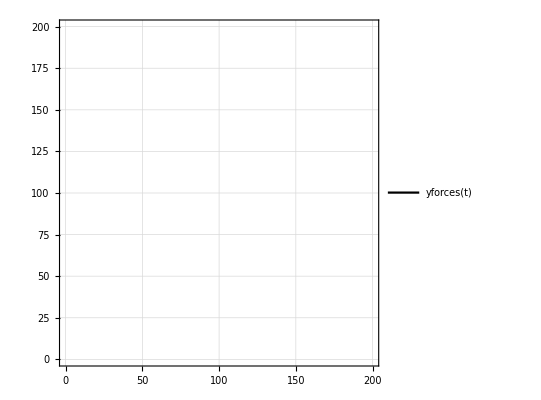

```mathematica
ParametricPlot[{yforces[t]},{t,0,1},PlotTheme->"Detailed"]
```

```mathematica
diffforces = ParametricNDSolveValue[{c'[t] == G2[c[t] - x11[t]].f1[t] + G2[c[t] - x21[t]].f2[t], c[0] == {b1,b2}}, c[1]-c[0],{t, 0, 1}, {b1,b2}, Method -> "StiffnessSwitching"];
diffnoforces= ParametricNDSolveValue[{c'[t] == G2[c[t] - x11[t]].dx11[t] + G2[c[t] - x21[t]].dx21[t], c[0] == {b1,b2}}, c[1]-c[0],{t, 0, 1}, {b1,b2}, Method -> "StiffnessSwitching",WorkingPrecision -> 25,PrecisionGoal->25,AccuracyGoal->25];
```

```mathematica
Simplify[diffforces[y0[[1]],y0[[2]]]].y0
```

ParametricNDSolveValue::nlnum: The function value {0.000265165 ((9 (0.+0.225 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+9.025 Power[«2»]) (689.133 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»])))+0.000267775 ((9 (0.+0.474342 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((«1») (689.133 Power[«1»]-«1»))/(4 (-1551.97+Times[«2»])))+«21» ((«1»)/(«1»)+«1»)+0.000798079 ((9 (0.-3.00416 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.474342 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))),«1»} is not a list of numbers with dimensions {2} at {t$7369,c[t$7369],NDSolve`s$7387[t$7369],NDSolve`s$7393[t$7369],NDSolve`s$7400[t$7369],NDSolve`s$7392[t$7369],NDSolve`s$7394[t$7369],b1$7367,b2$7368} = {0.,{100.,100.},1,1,1,1,-1,100.,100.}.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.

```mathematica
Simplify[diffforces[y0[[1]],y0[[2]]]].({{0,-1},{1,0}}.y0)
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.

ParametricNDSolveValue::nlnum: The function value {2.65203×10^-6 ((9 (0.+0.225 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+9.025 Power[«2»]) (689.133 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»])))+2.65176×10^-6 ((9 (0.+0.474342 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((«1») (689.133 Power[«1»]-«1»))/(4 (-1551.97+Times[«2»])))+«21» ((«1»)/(«1»)+«1»)+7.95582×10^-6 ((9 (0.-3.00416 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.474342 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))),«1»} is not a list of numbers with dimensions {2} at {t$7369,c[t$7369],NDSolve`s$7387[t$7369],NDSolve`s$7393[t$7369],NDSolve`s$7400[t$7369],NDSolve`s$7392[t$7369],NDSolve`s$7394[t$7369],b1$7367,b2$7368} = {0.,{-9998.57,-9998.57},1,1,1,1,-1,-9998.57,-9998.57}.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

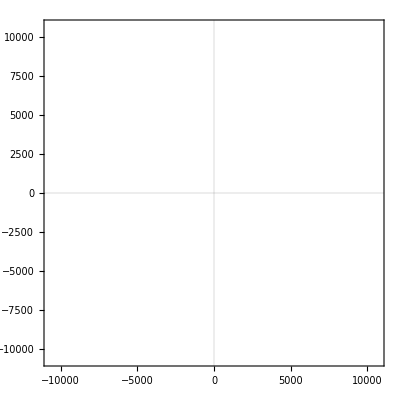

```mathematica
VectorPlot[diffforces[b1,b2],{b1,-10000,10000},{b2,-10000,10000},PlotTheme->"Scientific"]
```

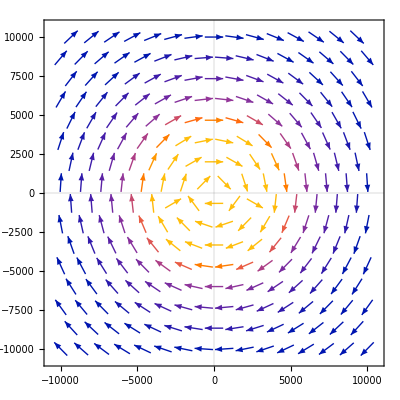

-Graphics-

```mathematica
dnftable=Table[{{b1,b2},diffnoforces[b1,b2]},{b1,-10000,10000,20000/15},{b2,-10000,10000,20000/15}];
ListVectorPlot[dnftable,PlotTheme->"Scientific"]
```

ParametricNDSolveValue::nlnum: The function value {0.+0.0149942 ((9 (0.+9.025 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.225 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»])))+0.018741 ((9 (0.-3.00416 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.474342 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))),0.+«21» ((«1»)/(«1»)+«1»)+0.0093705 ((9 (0.+0.474342 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.-3.00416 «1») («1»))/(4 (-1551.97+Times[«2»])))} is not a list of numbers with dimensions {2} at {t$7369,c[t$7369],NDSolve`s$7387[t$7369],NDSolve`s$7393[t$7369],NDSolve`s$7400[t$7369],NDSolve`s$7392[t$7369],NDSolve`s$7394[t$7369],b1$7367,b2$7368} = {0.,{10.0038,0.},1,1,1,1,-1,10.0038,0.}.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolveValue::nlnum: The function value {0.+0.0102155 ((9 (0.+9.025 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.225 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»])))+0.0118263 ((9 (0.-3.00416 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.474342 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))),0.+«21» ((«1»)/(«1»)+«1»)+0.00591313 ((9 (0.+0.474342 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.-3.00416 «1») («1»))/(4 (-1551.97+Times[«2»])))} is not a list of numbers with dimensions {2} at {t$7369,c[t$7369],NDSolve`s$7387[t$7369],NDSolve`s$7393[t$7369],NDSolve`s$7400[t$7369],NDSolve`s$7392[t$7369],NDSolve`s$7394[t$7369],b1$7367,b2$7368} = {0.,{14.6836,0.},1,1,1,1,-1,14.6836,0.}.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

ParametricNDSolveValue::nlnum: The function value {0.+0.00695971 ((9 (0.+9.025 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.225 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»])))+0.0076716 ((9 (0.-3.00416 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.474342 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))),0.+«21» («1»)+0.0038358 ((9 (0.+0.474342 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.-3.00416 «1») («1»))/(4 (-1551.97+Times[«2»])))} is not a list of numbers with dimensions {2} at {t$7369,c[t$7369],NDSolve`s$7387[t$7369],NDSolve`s$7393[t$7369],NDSolve`s$7400[t$7369],NDSolve`s$7392[t$7369],NDSolve`s$7394[t$7369],b1$7367,b2$7368} = {0.,{21.5526,0.},1,1,1,1,-1,21.5526,0.}.

General::stop: Further output of ParametricNDSolveValue::nlnum will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

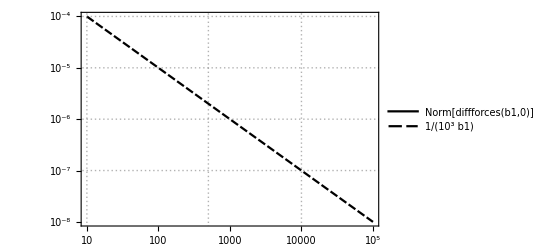

```mathematica
LogLogPlot[{Norm[diffforces[b1,0]],10^(-3)b1^(-1)},{b1,10,100000},PerformanceGoal->"Speed",PlotTheme->"Detailed"]
```

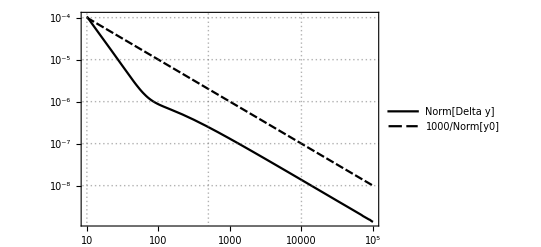

-Graphics-

```mathematica
intf=NIntegrate[{f1[t]+f2[t]},{t,0,1}][[1]]//ScientificForm
Simplify[(G2[{p,q}/((p^2+q^2)^(1/2))].intf)/Norm[{p,q}]]//ScientificForm
```

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{NIntegrate[((-81 a^4 ((Piecewise[{{Mod[t,1], 0≤Mod[t,1]≤1/4}, {1/4, 1/4≤Mod[t,1]≤1/2}, {3/4-Mod[t,1], 1/2≤Mod[t,1]≤3/4}, {0, True}}])^2+(2-({ | 1))^2)+18 a^2 (({ | 1)^2+2 (2-({ | 1))^2)^2) (-(4 ({ | 1) (2 1+1)^2)/(9 a^2 (({ | 1)^2+(2-1)^2))-(2 ({ | 1)11 (1))/(3 a √(1+1))))/(4 (9 a^2 (5 (Piecewise[{{Mod[t,1], 0≤Mod[t,1]≤1/4}, {1/4, 1/4≤Mod[t,1]≤1/2}, {3/4-Mod[t,1], 1/2≤Mod[t,1]≤3/4}, {0, True}}])^4+6 ({ | 1)^2 (2-({ | 1))^2+5 (2-({ | 1))^4)-8 (({ | 1)^6+4 ({ | 1)^4 (2-({ | 1))^2+4 ({ | 1)^2 (2-({ | 1))^4+(2-({ | 1))^6)))+1/(4 1)+1+(9 2 (1/1-1))/(4 (1)),{1}],1}
 |  |  |  |

NIntegrate::inumr: The integrand … has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

({{(3 (2 p^2+q^2))/(40 (p^2+q^2)),(3 p q)/(40 (p^2+q^2))},{(3 p q)/(40 (p^2+q^2)),(3 (p^2+2 q^2))/(40 (p^2+q^2))}}.{NIntegrate[((-81 a^1 (1^2+1)+1) 1)/(4 (9 a^2 (1)-8 (1)))+1+1+1/1,1],1})/(√(Abs[p]^2+Abs[q]^2))
 |  |  |  |

```mathematica
diffforcesapprox[p_,q_]={(("8.28375"×10^("-5")) p^("2")-("1.10262"×10^("-4")) p q+("4.14187"×10^("-5")) q^("2"))/((p^("2")+q^("2")) √(Abs[p]^("2")+Abs[q]^("2"))),(("-1.10262"×10^("-4")) p^("2")+("4.14187"×10^("-5")) p q-("2.20525"×10^("-4")) q^("2"))/((p^("2")+q^("2")) √(Abs[p]^("2")+Abs[q]^("2")))};
```

ParametricNDSolveValue::nlnum: The function value {0.+0.0149947 ((9 (0.+9.025 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.225 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»])))+0.0187417 ((9 (0.-3.00416 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.+0.474342 Power[«2»]) (2056.01 Power[«2»]-455.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))),0.+«21» ((«1»)/(«1»)+«1»)+0.00937084 ((9 (0.+0.474342 Power[«2»]) a^2 (-5.69531+50.625 Power[«2»]))/(4 (-1551.97+Times[«2»]))+((0.-3.00416 «1») («1»))/(4 (-1551.97+Times[«2»])))} is not a list of numbers with dimensions {2} at {t$7369,c[t$7369],NDSolve`s$7387[t$7369],NDSolve`s$7393[t$7369],NDSolve`s$7400[t$7369],NDSolve`s$7392[t$7369],NDSolve`s$7394[t$7369],b1$7367,b2$7368} = {0.,{10.0036,0.},1,1,1,1,-1,10.0036,0.}.

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

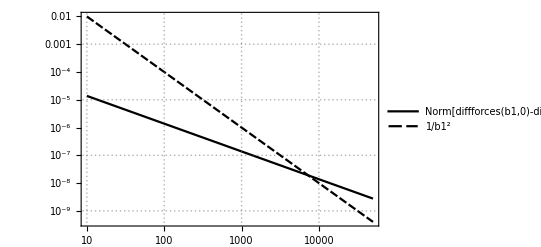

```mathematica
LogLogPlot[{Norm[diffforces[b1,0]-diffforcesapprox[b1,0]],1/(b1^2)},{b1,10,50000},PerformanceGoal->"Speed",PlotTheme->"Detailed"]
```

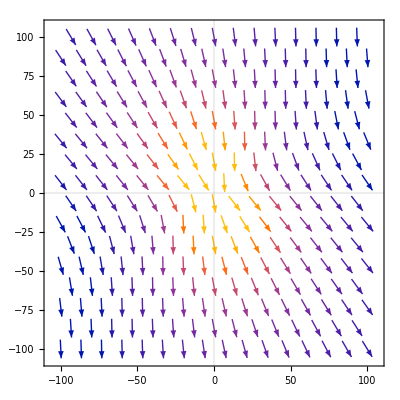

```mathematica
VectorPlot[diffforcesapprox[p,q],{p,-100,100},{q,-100,100},PlotTheme->"Scientific"]
```

```mathematica
ClearAll["Global"]
K2[t_]=Inverse[{{1,0,G2[x1[t]-x2[t]][[1,1]],G2[x1[t]-x2[t]][[1,2]]},
{0,1,G2[x1[t]-x2[t]][[2,1]],G2[x1[t]-x2[t]][[2,2]]},
{G2[x1[t]-x2[t]][[1,1]],G2[x1[t]-x2[t]][[1,2]],1,0},
{G2[x1[t]-x2[t]][[2,1]],G2[x1[t]-x2[t]][[2,2]],0,1}}];
Dimensions[K2[t]]
ff[t_]=K2[t].Join[dx1[t],dx2[t]];
```

{4,4}

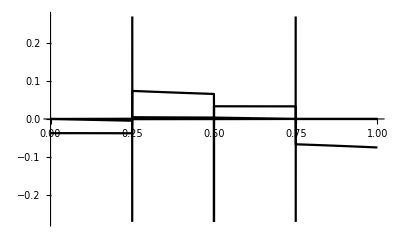

```mathematica
Plot[ff[t],{t,0,1}]
```

```mathematica
Plot[Join[f1[t],f2[t]],{t,0,1}]
```

-Graphics-